## Calculation

Preparations

```mathematica
wp = 25; ag = 20; pg = 20;
$Assumptions = {qt < Sqrt[2], qt > 0};

f[u_]:= 1 - (1+qt^2) u^2+qt^2 u^3
myPhiEq:=-(((f[u]-u (f')[u]) (phi')[u])/(u f[u]))+(phi[u] (ω^2-k^2 f[u]))/(4 rH^2 u f[u]^2)+(phi'')[u];

myphiEqRS = Collect[FullSimplify[myPhiEq /. {ω->rH w,k->rH kk}],{phi''[u],phi'[u],phi[u]}];
```

Horizon Expansion

```mathematica
order=8;
phiH[u_]:=(1-u)^((I w)/(2 (-2+qt^2))) Sum[cphiH[nn] (1-u)^nn,{nn,0,order}] /. {α->(I w)/(2 (-2+qt^2))}

ruleH=Get["/home/finn/Documents/studienprojekt/paper_notebooks/ruleHk14"]; 
phiHExpansion[u_,c0_]:=SetPrecision[phiH[u]/.ruleH/.{cphiH[0]->c0,cphiH[order]->0}, 25] /. {q->qt}
```

Solve DEQ

```mathematica
epsilon=1/1000000000; uBnum=epsilon;uHnum=1-1/10;

Clear[solphi]
solphi[omega_?NumericQ,kay_,c0_]:=
Block[
{w=omega,kk=kay},
Print[w, kk];
	NDSolve[{
			0==myphiEqRS,
			phi[uHnum]==phiHExpansion[uHnum,c0],
			phi'[uHnum]==(D[phiHExpansion[u,c0],u]/.{u->uHnum})
		},
		phi[u],{u,uBnum,uHnum},
		WorkingPrecision->wp,AccuracyGoal->ag,PrecisionGoal->pg,MaxSteps->100000]]

(* Usage: phiSol(w, k) *)
phiSol[w_?NumericQ, kk_]:=SetPrecision[solphi[w,kk,1][[1,1,2]],wp]
```

3.11945-2.74668 ⅈ0

NDSolve::precw: The precision of the differential equation ({{0==((0.546688-4.28406 ⅈ) phi[u])/((-1+u)^2 u (1+u)^2)+((-1-u) (-1-Power[«2»]) phi'[u])/((-1+u) u (1+u)^2)+((-1+Times[«2»])^2 phi''[u])/(1+u)^2,phi[9/10]==-0.78528405527915519841313+4.04901439894011662512603 ⅈ,phi'[9/10]==-39.724456622272896011243+28.478032776719278567636 ⅈ},{},{},{},{}}) is less than WorkingPrecision (25.).

5.6674816508033971240092×10^-10+2.90904567870719849415725×10^-9 ⅈ

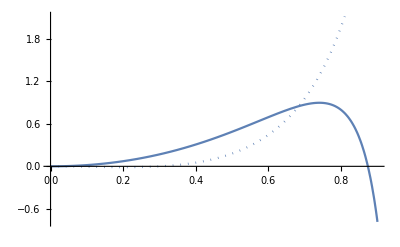

```mathematica
Block[{qt = 0},
	sol = phiSol[3.1194516 -2.7466757ⅈ, 0];
	sol /. u->(uBnum) // Print;
	ReImPlot[phi[u] /.{phi[u] -> sol}, {u, uBnum, uHnum}]]
```

Calculate QNM

```mathematica
qnmRoutine[initWR_,initWI_,kay_,kuh_]:=Block[
	{iWR=initWR,iWI=initWI,kk=kay,qt=kuh},
	
	eqQNMVBC[wR_?NumericQ,wI_?NumericQ]:=SetPrecision[Block[{w=wR+I wI},phiSol[w,kk]/.u->uBnum],wp];
	findQNMVBC[reWi_?NumericQ,imWi_?NumericQ]:=
		FindRoot[
			{Re[eqQNMVBC[wr,wi]]==0, Im[eqQNMVBC[wr,wi]]==0},
			{wr,reWi},
			{wi,imWi},
			WorkingPrecision->wp,
			AccuracyGoal->500,
			PrecisionGoal->500
		];
	qnmVBC=SetPrecision[findQNMVBC[iWR,iWI], wp];
	Print[{qnmVBC[[1,2]],qnmVBC[[2,2]]}]
]
```

```mathematica
qnmRoutine[0.05, -0.01, 1/2, Sqrt[2]*999/1000]
```

0.05-0.01 ⅈ 1/2

NDSolve::precw: The precision of the differential equation ({{0==(((0.0024-0.001 ⅈ)-1/4 Plus[«2»] Plus[«2»]) phi[u])/(4 (-1+u)^2 u (1+u+Times[«2»])^2)+((-1+u Plus[«2»]) (-1+Power[«2»] Plus[«2»]) phi'[u])/((-1+u) u (1+u+Times[«2»])^2)+((-1+Times[«2»])^2 phi''[u])/(1+u+Times[«2»])^2,phi[9/10]==1.19216×10^38-4.8923×10^36 ⅈ,phi'[9/10]==-7.74042×10^39+7.78493×10^39 ⅈ},{},{},{},{}}) is less than WorkingPrecision (25.).

0.05-0.01 ⅈ 1/2

NDSolve::precw: The precision of the differential equation ({{0==(((0.0024-0.001 ⅈ)-1/4 Plus[«2»] Plus[«2»]) phi[u])/(4 (-1+u)^2 u (1+u+Times[«2»])^2)+((-1+u Plus[«2»]) (-1+Power[«2»] Plus[«2»]) phi'[u])/((-1+u) u (1+u+Times[«2»])^2)+((-1+Times[«2»])^2 phi''[u])/(1+u+Times[«2»])^2,phi[9/10]==1.19216×10^38-4.8923×10^36 ⅈ,phi'[9/10]==-7.74042×10^39+7.78493×10^39 ⅈ},{},{},{},{}}) is less than WorkingPrecision (25.).

0.05-0.01 ⅈ 1/2

NDSolve::precw: The precision of the differential equation ({{0==(((0.0024-0.001 ⅈ)-1/4 Plus[«2»] Plus[«2»]) phi[u])/(4 (-1+u)^2 u (1+u+Times[«2»])^2)+((-1+u Plus[«2»]) (-1+Power[«2»] Plus[«2»]) phi'[u])/((-1+u) u (1+u+Times[«2»])^2)+((-1+Times[«2»])^2 phi''[u])/(1+u+Times[«2»])^2,phi[9/10]==1.19216×10^38-4.8923×10^36 ⅈ,phi'[9/10]==-7.74042×10^39+7.78493×10^39 ⅈ},{},{},{},{}}) is less than WorkingPrecision (25.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

0.05-0.01 ⅈ 1/2

0.05-0.00999999 ⅈ 1/2

0.05000000000000000277555756-0.01000000000000000020816682 ⅈ 1/2

FindRoot::bddir: The search direction {1.184413902308999540618876×10^-8,2.691013530063233102224018×10^-10} is not a descent direction for the merit function. The step will be taken without the line search.

0.05000001184413902586555297-0.009999999730898647201843507 ⅈ 1/2

0.05000001184413902586555297-0.009999999730898647201843507 ⅈ 1/2

0.05000001184445525363156981-0.009999999730898647201843507 ⅈ 1/2

0.05000001184413902586555297-0.009999999730582419435826668 ⅈ 1/2

Divide::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Divide::infy: Infinite expression 1/0 encountered.

FindRoot::jsing: Encountered a singular Jacobian at the point {wr,wi} = {0.05000001184413902586555297,-0.009999999730898647201843507}. Try perturbing the initial point(s).

{0.05000001184413902586555297,-0.009999999730898647201843507}